# Community detection in Lambda graphon

We demonstrate how to derive analytical expressions of the optimal community structure for the lambda graphon.
First, we define the graphon (L indicated the lambda parameter)

```mathematica
graphon[x_,y_] = (1-L)*x*y + L
```

L+(1-L) x y

The degree is found by integrating the graphon along the y axis.

```mathematica
degree=  Integrate[graphon[x,y],{y,0,1}]
```

L+1/2 (1-L) x

The edge density is found by integrating the degree along the x axis

```mathematica
Integrate[degree,{x,0,1}]
```

(1-L)/4+L

The modularity surface is the graphon minus the null model

```mathematica
B = Simplify[graphon [x,y] - (L+1/2 (1-L) x )*(L+1/2 (1-L) y)/((1-L)/4+L)]
```

-((-1+L) L (-1+2 x) (-1+2 y))/(1+3 L)

The modularity sliver is the double integral over it

```mathematica
Integrate[Integrate[B,{y,a,b}],{x,a,b}]
```

-((a-b)^2 (-1+a+b)^2 (-1+L) L)/(1+3 L)

The modularity for a two-community assignment

```mathematica
QTwoCommunities=-(((0-x)^2 (-1+0+x)^2 (-1+L) L)/(1+3 L)) + -(((x-1)^2 (-1+x+1)^2 (-1+L) L)/(1+3 L))
```

-(2 (-1+L) L (-1+x)^2 x^2)/(1+3 L)

Necessary condition for extremum

```mathematica
Solve[D[QTwoCommunities,x]==0]
```

```mathematica
{{L->0},{L->1},{x->0},{x->1/2},{x->1}}
```

Plot second derivative to demonstrate that it is a minimum at x=1/2

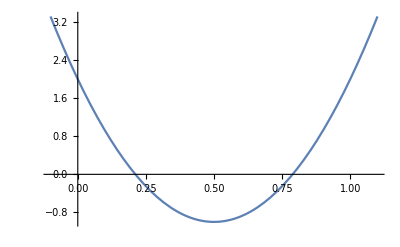

```mathematica
Plot[2 (-1+x)^2+8 (-1+x) x+2 x^2,{x,-0.1,1.1}]
```